```mathematica
ωdef[s_,I_,d_,T_]:=s*Exp[(d-I)*T]
```

```mathematica
F[ω_,σ_]:=1/2(1+Erf[(-Log[ω]-σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
Fc[ω_,σ_]:=1/2(1-Erf[(-Log[ω]+σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
rhs1[s_,I_,d_,T_,σ_]:=s*Exp[d*T]*F[ωdef[s,I,d,T],σ]
```

```mathematica
rhs1[s_,I_,d_,T_,σ_]:=s*Exp[d*T]*1/2(1+Erf[((I-d)*T-Log[s]-σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
rhs2[s_,I_,d_,T_,σ_]:=Exp[I*T]*Fc[ωdef[s,I,d,T],σ]
```

```mathematica
rhs2[s_,I_,d_,T_,σ_]:=Exp[I*T]*1/2(1-Erf[((I-d)*T-Log[s]+σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
lhs[s_,f_,T_]:=s*Exp[f*T]
```

```mathematica
rd[s_?NumericQ,I_?NumericQ,f_?NumericQ,T_?NumericQ,σ_?NumericQ]:=d/. FindRoot[0==-lhs[s,f,T]+rhs1[s,I,d,T,σ]+rhs2[s,I,d,T,σ],{d,0.015,0.,0.999},AccuracyGoal->8,PrecisionGoal->8,MaxIterations->1000 (*Guess,Min,Max*)]
```

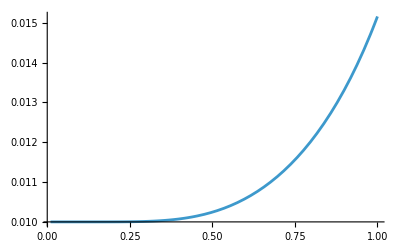

```mathematica
Plot[rd[s,0.02,0.01,30,0.5],{s,0.01,1.0}]
```

```mathematica
Fe[ω_,σ_]:=1/2(1+Erf[(-Log[ω]+σ^2/2)/(σ*Sqrt[2])])
```

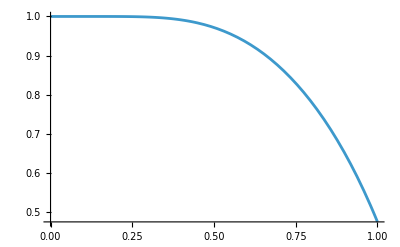

```mathematica
Plot[Fe[ωdef[s,0.015,rd[s,0.015,0.01,30,0.5],30],0.5],{s,0.0,1.0}]
```

```mathematica
Fec[ω_,σ_]:=1/2(1+Erf[(-Log[ω]-σ^2/2)/(σ*Sqrt[2])])
```

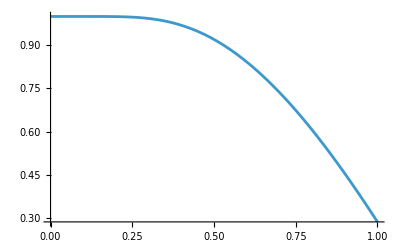

```mathematica
Plot[Fec[ωdef[s,0.015,rd[s,0.015,0.01,30,0.5],30],0.5],{s,0.0,1.0}]
```

```mathematica
ExpET[s_,I_,d_,T_,σ_]:=Exp[I*T]/(1-s)*Fe[ωdef[s,I,d,T],σ]-(s*Exp[d*T])/(1-s)*Fec[ωdef[s,I,d,T],σ]
```

```mathematica
ExpETnum[s_?NumericQ,I_?NumericQ,f_?NumericQ,T_?NumericQ,σ_?NumericQ]:=ExpET[s,I,rd[s,I,f,T,σ],T,σ]
```

```mathematica
Plot[ExpETnum[0.8,0.02,0.01,30,σ],{σ,0.01,1.0}]
```

-Graphics-

```mathematica
EquityReturn[s_?NumericQ,I_?NumericQ,f_?NumericQ,T_?NumericQ,σ_?NumericQ]:=(1-s)*ExpETnum[s,I,f,T,σ]
```

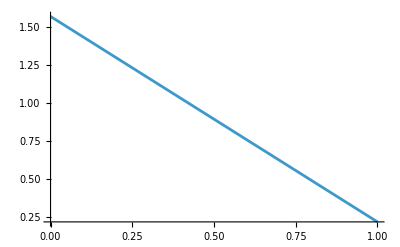

```mathematica
Plot[EquityReturn[s,0.015,0.01,30,1],{s,0.0,1.0}]
```

```mathematica
e[s_,I_,d_,T_,σ_]:=Log[ExpET[s,I,d,T,σ]]/T
```

```mathematica
enum[s_?NumericQ,I_?NumericQ,f_?NumericQ,T_?NumericQ,σ_?NumericQ]:=FractionBox[Log[ExpET[s,I,rd[s,I,f,T,σ],T,σ]],T]
```

```mathematica
re[I_,f_,T_,σ_]:=NMaximize[{enum[s,I,f,T,σ],0.001<=s<=0.999},s,AccuracyGoal->8,PrecisionGoal->8,MaxIterations->1000]
```

```mathematica
ExpWACCTnum[s_?NumericQ,I_?NumericQ,f_?NumericQ,T_?NumericQ,σ_?NumericQ]:=s*Exp[rd[s,I,f,T,σ]*T]+(1-s)*ExpETnum[s,I,f,T,σ]
```

```mathematica
ExpWACCTnum[0.5,0.02,0.01,30,0.3]
```

1.82216

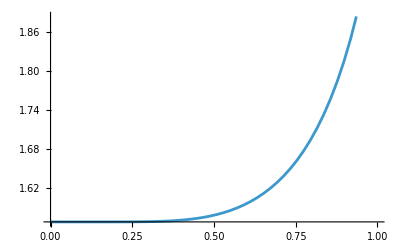

```mathematica
Plot[ExpWACCTnum[s,0.015,0.01,30,0.5],{s,0.0,1.0}]
```

```mathematica
WACCnum[s_?NumericQ,I_?NumericQ,f_?NumericQ,T_?NumericQ,σ_?NumericQ]:=Log[ExpWACCTnum[s,I,f,T,σ]]/T
```

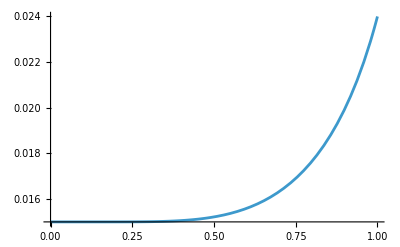

```mathematica
Plot[WACCnum[s,0.015,0.01,30,0.5],{s,0.0,1.0}]
```

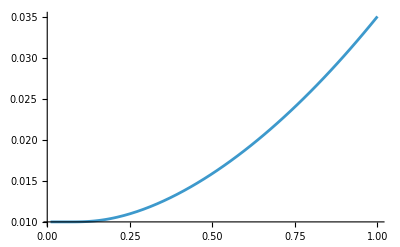

```mathematica
Plot[WACCnum[0.8,0.01,0.01,30,σ],{σ,0.01,1.0},PlotRange->Full]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

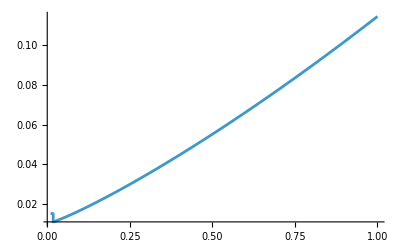

```mathematica
Plot[WACCnum[0.999,0.01,0.01,30,σ],{σ,0.01,1.0},PlotRange->Full]
```